(.1a)^4

.1a

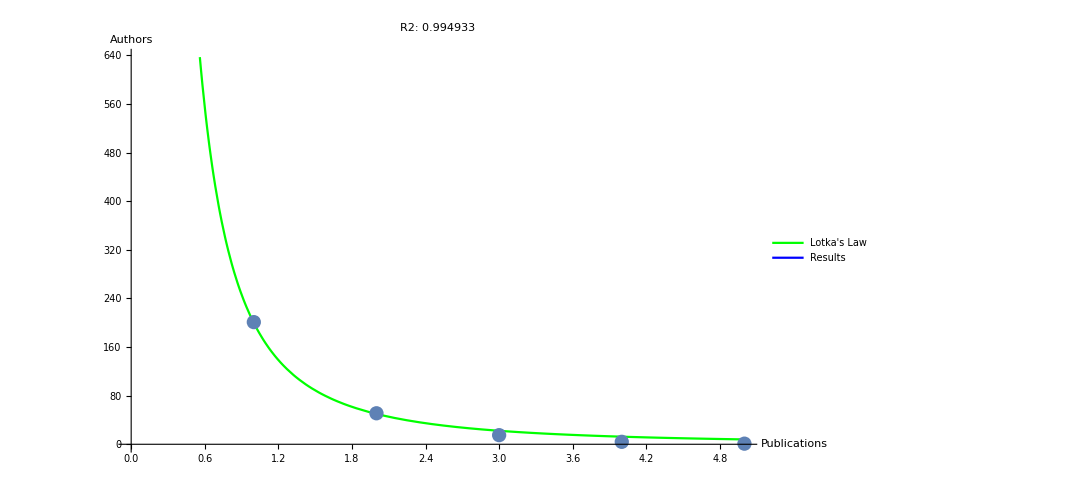

```mathematica
dataPublicationsCurve = Import["/home/fabianact/Tesis/Pruebas/Model/testTables/10-100-0.01-0.01-turtles.csv"];
fitFkt=NonlinearModelFit[dataPublicationsCurve,a / x^2,{a},x];.1a.1a.1a.1a
fit= Plot[fitFkt[x],{x,0,Max[dataPublicationsCurve[[All,1]]]}, ImageSize->800, PlotStyle->Green];.1a
R2=fitFkt["AdjustedRSquared"];
plot=Show[fit,ListPlot[dataPublicationsCurve,ImageSize->800], AxesLabel->{"Publications","Authors"}, PlotLabel->"R2: " <> ToString[R2]];
plotTotal = Legended[plot,LineLegend[{Green,Blue},{"Lotka's Law","Results"}]]
Export["Lotka-data.png",plotTotal];
```